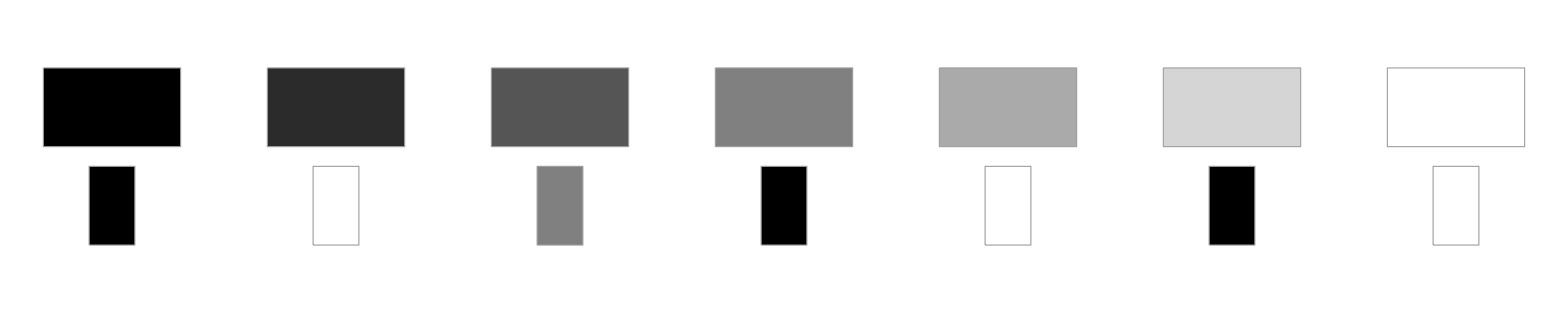

-Graphics-

```mathematica
(* Current progress: Automate?
Image
Tranlating
Annotating
Realistic?
*)
Clear["`*"]
(*See http://en.wikipedia.org/wiki/Cellular_automaton *)
dim=1000;
dim2=dim/2;
seed =Table[0,{dim}];
seed[[dim2]]=1;
(*Source code: http://mathworld.wolfram.com/TotalisticCellularAutomaton.html*)
r=1599;
n=100;
RulePlot[CellularAutomaton[{r,{3,1}}]]
ArrayPlot[CellularAutomaton[{r,{3,1}},{{1},0},n,{All,All}]]
(*Animate[ArrayPlot[CellularAutomaton[{r,{3,1}},{{1},0},n,{All,All}]],{n,4000,8000,1},AnimationRunning->False]*)

(*ArrayPlot[CellularAutomaton[30,seed,4000]]*)

(* This command  will give the same plot : ArrayPlot[CellularAutomaton[30,{{1},0},1000]]. CellularAutomaton is thus a command in Mathematica *)(*
 Animate[ArrayPlot[CellularAutomaton[400,{{1},0},n]],{n,1,100,1},AnimationRunning->False]*)
```